```mathematica
Clear[nth,r,probSTV]
```

```mathematica
probSTV[n_]=((Sqrt[nth^2 *(1+nth)^2-(2*nth+1)^2*Sinh[r]^2*Cosh[r]^2])^n)/(((1+nth)^2+(2*nth+1)*Sinh[r]^2)^(n+1/2))*LegendreP[n,(nth*(1+nth))/Sqrt[nth^2 *(1+nth)^2-(2*nth+1)^2*Sinh[r]^2*Cosh[r]^2]];
```

```mathematica
∑_(n=0)^∞ probSTV[n]
```

1.+0. ⅈ

```mathematica
nth=0.2;
r=0.3;
```

```mathematica
probSTV[2]
```

0.050817

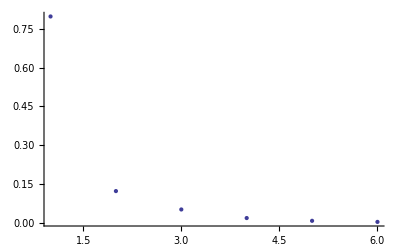

```mathematica
ListPlot[Table[probSTV[n],{n,0,5}]]
```